# Variance of Renyi-2 entropy

### Clear all variables

```mathematica
Remove["GLO`*"];
Remove["Global`*"];
```

### Import GLO package

```mathematica
Get["~/Documents/Wolfram Mathematica/GLO/functions/GLO.wl"];
```

## Simulation

### Choose system sizes to simulate

```mathematica
ns=Range[400,1000,100];
```

### Choose partition scales to simulate

```mathematica
rs=Range[.1,.5,.05];
partitionSize[n_,r_]:=Ceiling[r n];
```

### Squeezing parameter for each mode

```mathematica
s=.1;
squeeze[n_]:=Table[s,n];
```

### Choose how many simulations to run in order to estimate the average

```mathematica
iters[n_]:=50;
```

### Simulate

```mathematica
variances=Module[{σ0,u,σ,entropyData,data},
Table[
Print["started ", n];
(*initialize product squeezed state*)
σ0=initialSqueezedState@squeeze[n];
entropyData=Table[
(*haar random passive lo unitary*)
u=haarModeMatrix@n;
(*apply to initial state*)
σ=σ0~applyByCongruence~u;
(*renyi2 entropy of a partition of size n^r*)
Table[
renyi2EntropyOfLeftPartition[σ,partitionSize[n,r]],{r,rs}
],
{i,iters[n]}];
(* variances/mean^2 *)
data=Variance[entropyData];(*/Mean[entropyData]^2;*)
(* Now for plotting, add in the x-axis *)
Do[
data[[i]]={rs[[i]],data[[i]]};,
{i,Length@rs}
];
data,
{n,ns}
]
];
```

started 400

started 500

started 600

started 700

started 800

started 900

started 1000

### Plot results

```mathematica
plot[plotFun_:ListPlot]:=plotFun[variances,
BaseStyle->{FontSize->16},
AxesLabel->{"partition fraction r","Var(S_2)"},
PlotLegends->Table["num modes: " <> ToString@n,{n,ns}],
ImageSize->Large,
PlotRange->All,
Joined->True
(*PlotMarkers->Automatic*)
];
```

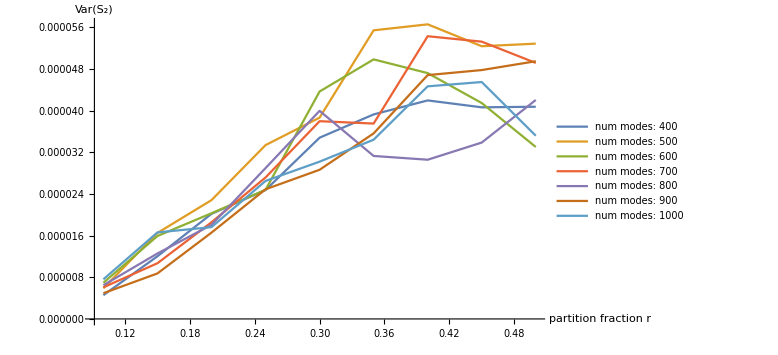

```mathematica
plot[ListPlot]
```

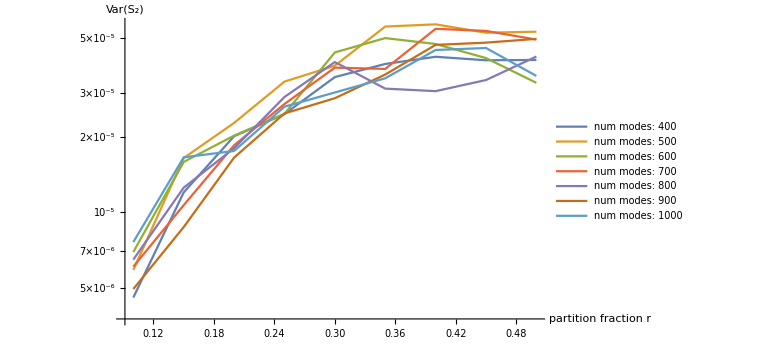

```mathematica
plot[ListLogPlot]
```

### Plot with our analytic formula using ω^(2)=1/2 that is correct for small s

```mathematica
guess[plotFun_:ListPlot]:=plotFun[
Table[{r,1/2 Tanh[2s]^4(r(1-r))^2},{r,rs}],
Joined->True,
PlotStyle->{Thick,Dashed,Black}
];
```

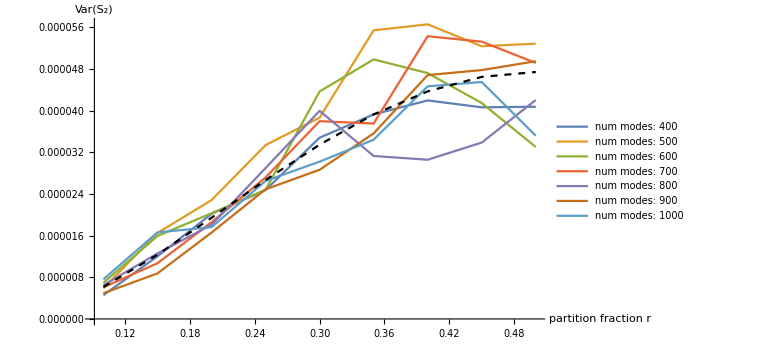

```mathematica
Show[plot[ListPlot],guess[ListPlot]]
```

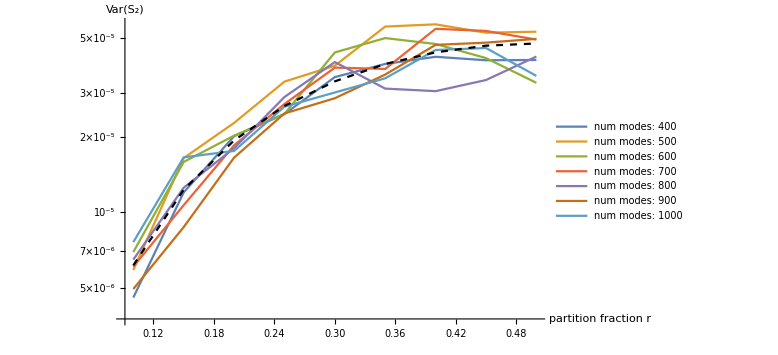

```mathematica
Show[plot[ListLogPlot],guess[ListLogPlot]]
```

### Plot restructured

```mathematica
variancesR=Table[
Table[{ns[[i]],variances[[i,j,2]]},{i,Length@ns}],
{j,Length@rs}
];
```

```mathematica
plotR[plotFun_:ListPlot]:=plotFun[variancesR,
BaseStyle->{FontSize->16},
AxesLabel->{"number of modes n","Var(S_2)"},
PlotLegends->Table["r: " <> ToString@r,{r,rs}],
ImageSize->Large,
PlotRange->All,
Joined->True
(*PlotMarkers->Automatic*)
];
```

```mathematica
guessR[plotFun_:ListPlot]:=plotFun[Table[
Table[{n,1/2 Tanh[2s]^4(r(1-r))^2},{n,ns}],
{r,rs}
],
Joined->True,
PlotStyle->Table[{Thick,Dashed},Length@rs]
];
```

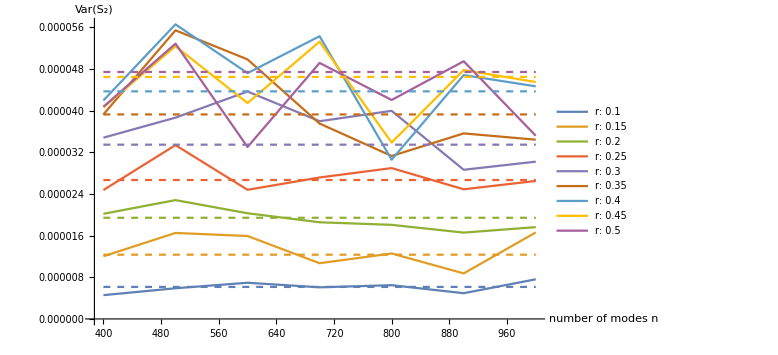

```mathematica
Show[plotR[ListPlot],guessR[ListPlot]]
```

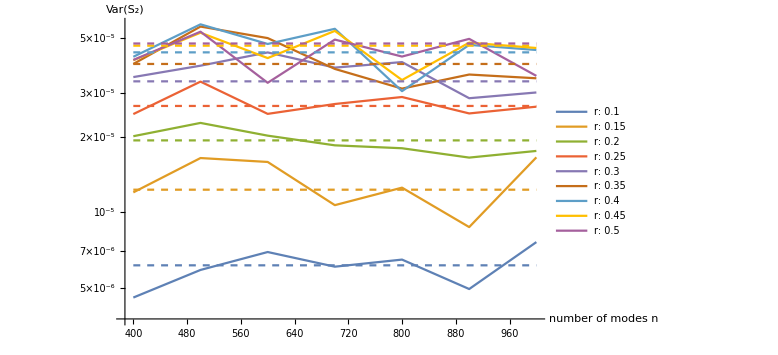

```mathematica
Show[plotR[ListLogPlot],guessR[ListLogPlot]]
```